```mathematica
$Assumptions=Element[w,Reals] && Element[k, Reals]&& Element[t, Reals]&& Element[x, Reals]&& Element[m, Reals]
```

w∈Reals&&k∈Reals&&t∈Reals&&x∈Reals&&m∈Reals

```mathematica
phi[x_,t_,k_]:=(a[k]+I b[k])*Exp[-I*(w t-k x)]+(a[k]-I b[k])*Exp[I*(w t-k x)]+S[k]/(k^2+m^2)*Exp[I k x]
```

```mathematica
pi[x_,t_,k_]:=D[phi[x,t,k],t]
```

```mathematica
pi[x,t,k]
```

ⅈ ⅇ^(ⅈ (t w-k x)) w (a[k]-ⅈ b[k])-ⅈ ⅇ^(-ⅈ (t w-k x)) w (a[k]+ⅈ b[k])

```mathematica
Expand[pi[x,t,k]*pi[x,t,ks]+D[phi[x,t,k],x]D[phi[x,t,ks],x]+m^2 phi[x,t,k]*phi[x,t,ks]+S[k] Phi[x,t,ks]]
```

-ⅇ^(-ⅈ (t w-k x)-ⅈ (t w-ks x)) k ks a[k] a[ks]+ⅇ^(ⅈ (t w-k x)-ⅈ (t w-ks x)) k ks a[k] a[ks]+ⅇ^(-ⅈ (t w-k x)+ⅈ (t w-ks x)) k ks a[k] a[ks]-ⅇ^(ⅈ (t w-k x)+ⅈ (t w-ks x)) k ks a[k] a[ks]+ⅇ^(-ⅈ (t w-k x)-ⅈ (t w-ks x)) m^2 a[k] a[ks]+ⅇ^(ⅈ (t w-k x)-ⅈ (t w-ks x)) m^2 a[k] a[ks]+ⅇ^(-ⅈ (t w-k x)+ⅈ (t w-ks x)) m^2 a[k] a[ks]+ⅇ^(ⅈ (t w-k x)+ⅈ (t w-ks x)) m^2 a[k] a[ks]-ⅇ^(-ⅈ (t w-k x)-ⅈ (t w-ks x)) w^2 a[k] a[ks]+ⅇ^(ⅈ (t w-k x)-ⅈ (t w-ks x)) w^2 a[k] a[ks]+ⅇ^(-ⅈ (t w-k x)+ⅈ (t w-ks x)) w^2 a[k] a[ks]-ⅇ^(ⅈ (t w-k x)+ⅈ (t w-ks x)) w^2 a[k] a[ks]-ⅈ ⅇ^(-ⅈ (t w-k x)-ⅈ (t w-ks x)) k ks a[ks] b[k]-ⅈ ⅇ^(ⅈ (t w-k x)-ⅈ (t w-ks x)) k ks a[ks] b[k]+ⅈ ⅇ^(-ⅈ (t w-k x)+ⅈ (t w-ks x)) k ks a[ks] b[k]+ⅈ ⅇ^(ⅈ (t w-k x)+ⅈ (t w-ks x)) k ks a[ks] b[k]+ⅈ ⅇ^(-ⅈ (t w-k x)-ⅈ (t w-ks x)) m^2 a[ks] b[k]-ⅈ ⅇ^(ⅈ (t w-k x)-ⅈ (t w-ks x)) m^2 a[ks] b[k]+ⅈ ⅇ^(-ⅈ (t w-k x)+ⅈ (t w-ks x)) m^2 a[ks] b[k]-ⅈ ⅇ^(ⅈ (t w-k x)+ⅈ (t w-ks x)) m^2 a[ks] b[k]-ⅈ ⅇ^(-ⅈ (t w-k x)-ⅈ (t w-ks x)) w^2 a[ks] b[k]-ⅈ ⅇ^(ⅈ (t w-k x)-ⅈ (t w-ks x)) w^2 a[ks] b[k]+ⅈ ⅇ^(-ⅈ (t w-k x)+ⅈ (t w-ks x)) w^2 a[ks] b[k]+ⅈ ⅇ^(ⅈ (t w-k x)+ⅈ (t w-ks x)) w^2 a[ks] b[k]-ⅈ ⅇ^(-ⅈ (t w-k x)-ⅈ (t w-ks x)) k ks a[k] b[ks]+ⅈ ⅇ^(ⅈ (t w-k x)-ⅈ (t w-ks x)) k ks a[k] b[ks]-ⅈ ⅇ^(-ⅈ (t w-k x)+ⅈ (t w-ks x)) k ks a[k] b[ks]+ⅈ ⅇ^(ⅈ (t w-k x)+ⅈ (t w-ks x)) k ks a[k] b[ks]+ⅈ ⅇ^(-ⅈ (t w-k x)-ⅈ (t w-ks x)) m^2 a[k] b[ks]+ⅈ ⅇ^(ⅈ (t w-k x)-ⅈ (t w-ks x)) m^2 a[k] b[ks]-ⅈ ⅇ^(-ⅈ (t w-k x)+ⅈ (t w-ks x)) m^2 a[k] b[ks]-ⅈ ⅇ^(ⅈ (t w-k x)+ⅈ (t w-ks x)) m^2 a[k] b[ks]-ⅈ ⅇ^(-ⅈ (t w-k x)-ⅈ (t w-ks x)) w^2 a[k] b[ks]+ⅈ ⅇ^(ⅈ (t w-k x)-ⅈ (t w-ks x)) w^2 a[k] b[ks]-ⅈ ⅇ^(-ⅈ (t w-k x)+ⅈ (t w-ks x)) w^2 a[k] b[ks]+ⅈ ⅇ^(ⅈ (t w-k x)+ⅈ (t w-ks x)) w^2 a[k] b[ks]+ⅇ^(-ⅈ (t w-k x)-ⅈ (t w-ks x)) k ks b[k] b[ks]+ⅇ^(ⅈ (t w-k x)-ⅈ (t w-ks x)) k ks b[k] b[ks]+ⅇ^(-ⅈ (t w-k x)+ⅈ (t w-ks x)) k ks b[k] b[ks]+ⅇ^(ⅈ (t w-k x)+ⅈ (t w-ks x)) k ks b[k] b[ks]-ⅇ^(-ⅈ (t w-k x)-ⅈ (t w-ks x)) m^2 b[k] b[ks]+ⅇ^(ⅈ (t w-k x)-ⅈ (t w-ks x)) m^2 b[k] b[ks]+ⅇ^(-ⅈ (t w-k x)+ⅈ (t w-ks x)) m^2 b[k] b[ks]-ⅇ^(ⅈ (t w-k x)+ⅈ (t w-ks x)) m^2 b[k] b[ks]+ⅇ^(-ⅈ (t w-k x)-ⅈ (t w-ks x)) w^2 b[k] b[ks]+ⅇ^(ⅈ (t w-k x)-ⅈ (t w-ks x)) w^2 b[k] b[ks]+ⅇ^(-ⅈ (t w-k x)+ⅈ (t w-ks x)) w^2 b[k] b[ks]+ⅇ^(ⅈ (t w-k x)+ⅈ (t w-ks x)) w^2 b[k] b[ks]-(ⅇ^(ⅈ k x-ⅈ (t w-ks x)) k ks a[ks] S[k])/(k^2+m^2)+(ⅇ^(ⅈ k x+ⅈ (t w-ks x)) k ks a[ks] S[k])/(k^2+m^2)+(ⅇ^(ⅈ k x-ⅈ (t w-ks x)) m^2 a[ks] S[k])/(k^2+m^2)+(ⅇ^(ⅈ k x+ⅈ (t w-ks x)) m^2 a[ks] S[k])/(k^2+m^2)-(ⅈ ⅇ^(ⅈ k x-ⅈ (t w-ks x)) k ks b[ks] S[k])/(k^2+m^2)-(ⅈ ⅇ^(ⅈ k x+ⅈ (t w-ks x)) k ks b[ks] S[k])/(k^2+m^2)+(ⅈ ⅇ^(ⅈ k x-ⅈ (t w-ks x)) m^2 b[ks] S[k])/(k^2+m^2)-(ⅈ ⅇ^(ⅈ k x+ⅈ (t w-ks x)) m^2 b[ks] S[k])/(k^2+m^2)+Phi[x,t,ks] S[k]-(ⅇ^(ⅈ ks x-ⅈ (t w-k x)) k ks a[k] S[ks])/(ks^2+m^2)+(ⅇ^(ⅈ ks x+ⅈ (t w-k x)) k ks a[k] S[ks])/(ks^2+m^2)+(ⅇ^(ⅈ ks x-ⅈ (t w-k x)) m^2 a[k] S[ks])/(ks^2+m^2)+(ⅇ^(ⅈ ks x+ⅈ (t w-k x)) m^2 a[k] S[ks])/(ks^2+m^2)-(ⅈ ⅇ^(ⅈ ks x-ⅈ (t w-k x)) k ks b[k] S[ks])/(ks^2+m^2)-(ⅈ ⅇ^(ⅈ ks x+ⅈ (t w-k x)) k ks b[k] S[ks])/(ks^2+m^2)+(ⅈ ⅇ^(ⅈ ks x-ⅈ (t w-k x)) m^2 b[k] S[ks])/(ks^2+m^2)-(ⅈ ⅇ^(ⅈ ks x+ⅈ (t w-k x)) m^2 b[k] S[ks])/(ks^2+m^2)-(ⅇ^(ⅈ k x+ⅈ ks x) k ks S[k] S[ks])/((k^2+m^2) (ks^2+m^2))+(ⅇ^(ⅈ k x+ⅈ ks x) m^2 S[k] S[ks])/((k^2+m^2) (ks^2+m^2))

```mathematica
pi
```

pi

```mathematica
Conjugate[I]
```

-ⅈ

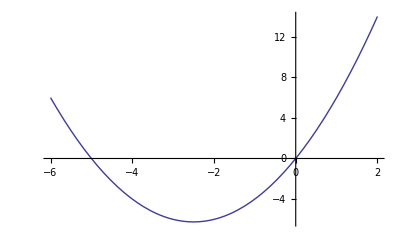

```mathematica
Plot[x^2+5*x,{x,-6,2}]
```

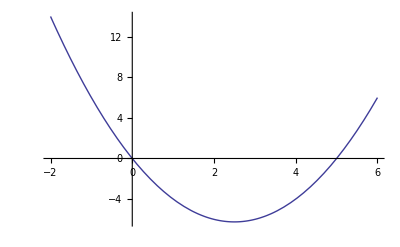

```mathematica
Plot[x^2-5*x,{x,-2,6}]
```

```mathematica
RevolutionPlot3D[t^4-t^2,{t,0,1.11},{theta,0,Pi},BoxRatios->{1,0.5,1}]
```

-Graphics3D-